```mathematica
卫星轨道计算
```

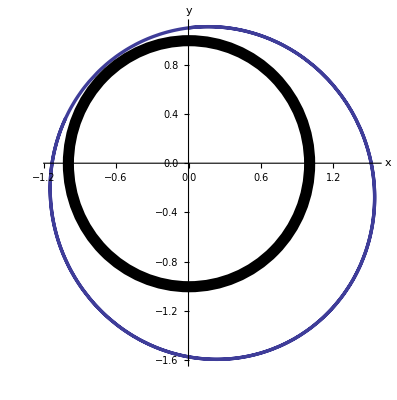

```mathematica
tm=3;coef=4.0 π^2;
xinitial={0,6.5};yinitial={1.1,0.8};
equ={x''[t]==-(coef*x[t])/((x[t]^2+y[t]^2)^(3/2)),
y''[t]==-(coef*y[t])/((x[t]^2+y[t]^2)^(3/2)),
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equ,{x,y},{t,0,tm}];
{x,y}={x,y}/.s[[1]];
ParametricPlot[{x[t],y[t]},{t,0,tm},
AxesLabel->{"x","y"},
BaseStyle->{FontSize->13},
PlotStyle->Thickness[0.006],
AxesStyle->Thickness[0.003],
Epilog->{Thickness[0.02],Circle[{0,0},1]}]
Clear[x,y,tm,xinitial,yinitial,s,equ,coef]
```